```mathematica
"definição do retângulo"
a=1
b=1
```

definição do retângulo

1

1

```mathematica
"definição da base utilizada"
φ[x_,y_,n_,m_]=x^n(x-a)y^m(y-b)
nM=2
mM=2
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
```

definição da base utilizada

(-1+x) x^n (-1+y) y^m

2

2

{(-1+x) x (-1+y) y,(-1+x) x^2 (-1+y) y,(-1+x) x (-1+y) y^2,(-1+x) x^2 (-1+y) y^2}

```mathematica
"definição da matriz A"
A[k_] = Table[∫_0^b ∫_0^a φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]Laplacian[φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{x,y}]ⅆxⅆy+k^2∫_0^b ∫_0^a φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM]ⅆxⅆy ,{i,0,nM*mM-1},{j,0,nM*mM-1}]
A[k] // MatrixForm
```

definição da matriz A

```mathematica
"autovalores obtidos numericamente"
Solve[Det[A[k]]== 0 && k ≥ 0,k]
```

autovalores obtidos numericamente

{{k→2 √5},{k→2 √13},{k→2 √13},{k→2 √21}}

```mathematica
"autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia"
ka=2 √13
Vc[ka]=NullSpace[A[ka]]
id=2
v=Vc[ka][[id]]
ϕ[x_,y_]=Base[x,y].v
```

autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia

2 √13

{{-1/2,0,1,0},{-1/2,1,0,0}}

2

{-1/2,1,0,0}

-1/2 (-1+x) x (-1+y) y+(-1+x) x^2 (-1+y) y

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,0,a},{y,0,b}]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

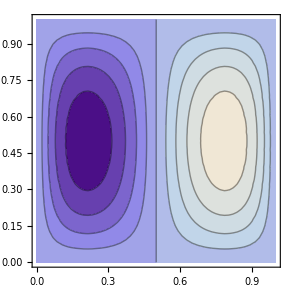

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,0,a},{y,0,b}]
```